```mathematica
Quit[]
```

#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Gravito-inertial modes with radial stratification

## Load fennec & spectral package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

## Equations

```mathematica
Needs["TenGSHui`","~/ownCloud/Shared/TenGSHui.m"];
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

```mathematica
Rank[ρ0]^=0;
MaxDegree[ρ0]^=0;
ρ0[][0,0][r_]:=Exp[logρ[r]]
```

```mathematica
Rank[𝒩2]^=0;
MaxDegree[𝒩2]^=0;
𝒩2[][0,0][r_]:=N2[r]
```

```mathematica
Rank[ξ]^=1;
MaxDegree[ξ]^=∞;
ξ[-1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)(P[ℓ,𝓂][r] (1/r+logρ'[r])+P[ℓ,𝓂]'[r]-ⅈ T[ℓ,𝓂][r])
ξ[0][ℓ_,𝓂_][r_]:=ℓ(ℓ+1)(P[ℓ,𝓂][r])/r
ξ[1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)(P[ℓ,𝓂][r] (1/r+logρ'[r])+P[ℓ,𝓂]'[r]+ⅈ T[ℓ,𝓂][r])
```

```mathematica
σ≐(-2/3)⋆(ξ)⊗𝕘⊕2⋆(∇ξ)
```

```mathematica
eq≐λ^2⋆ξ⊕(2Ω λ)⋆(𝟙[𝕫]ξ)⊕(𝒩2⊗(ξ·𝕖𝓇)⊗𝕖𝓇)⊕(-Ek λ)⋆σ
curleq≐λ^2⋆ξ⊕(-2Ω λ)⋆ξ𝟙[𝕫]⊕(-Ek λ)⋆(σ)
curlcurleq≐λ^2⋆ξ⊕(-2Ω λ)⋆ξ𝟙[𝕫]⊕(𝒩2⊗(ξ·𝕖𝓇)⊗𝕖𝓇)⊕(-Ek λ)⋆(σ)
```

```mathematica
N2[r_]:=N0 r^2
logρ[r_]:=(*-2Log[r] 10^-1*)0
```

## Call to sprouts

```mathematica
ℓmax=20;𝓂=0;parity=1;
If[(EvenQ[𝓂]&&SameQ[parity,1]),ℓmax+=1];
```

```mathematica
rangeℓ𝓂=DeleteCases[Table[{ℓ,𝓂},{ℓ,Abs[𝓂],ℓmax}],{0,0}];
Which[
parity==1,
rangeℓ𝓂P=DeleteCases[rangeℓ𝓂,{ℓ_,𝓂_}/;OddQ[ℓ]];
rangeℓ𝓂T=DeleteCases[rangeℓ𝓂,{ℓ_,𝓂_}/;EvenQ[ℓ]],
parity==-1,
rangeℓ𝓂P=DeleteCases[rangeℓ𝓂,{ℓ_,𝓂_}/;EvenQ[ℓ]];
rangeℓ𝓂T=DeleteCases[rangeℓ𝓂,{ℓ_,𝓂_}/;OddQ[ℓ]];
];
```

```mathematica
Block[{Ω=1,N0=0,Ek=0},
ℒ=Join[Table[Simplify[curlcurleq[0][Sequence@@i][r]],{i,rangeℓ𝓂P}],Table[Simplify[curleq[0][Sequence@@i][r]],{i,rangeℓ𝓂T}]];
ℬ=DeleteCases[Simplify@Join[Table[P[Sequence@@i][1]==0,{i,rangeℓ𝓂P}],Table[Ek P[Sequence@@i]'[1]==0,{i,rangeℓ𝓂P}],Table[Ek T[Sequence@@i][1]==0,{i,rangeℓ𝓂T}]],True];
𝒱=Join[Table[P[Sequence@@i],{i,rangeℓ𝓂P}],Table[T[Sequence@@i],{i,rangeℓ𝓂T}]];
]
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,0,1},100,eigenvalue->λ]
```

partition of the spatial domain :  {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :   (A0+A1 λ+A2 λ^2)x==0

Size of output matrices :  1050x1050

{SparseArray[…],SparseArray[…],SparseArray[…]}

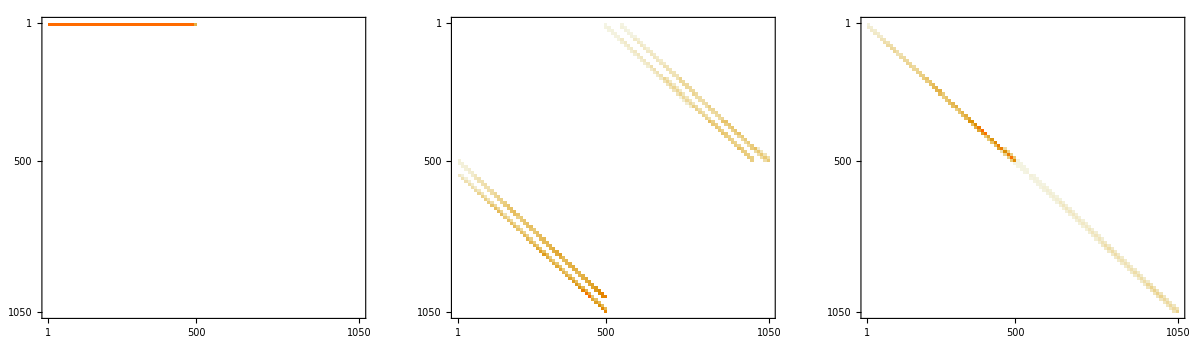

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

```mathematica
Export["../slepc/A0.mtx",A[[1]]/Norm[A[[3]],"Frobenius"]]
Export["../slepc/A1.mtx",A[[2]]/Norm[A[[3]],"Frobenius"]]
Export["../slepc/A2.mtx",A[[3]]/Norm[A[[3]],"Frobenius"]]
```

../slepc/A0.mtx

../slepc/A1.mtx

../slepc/A2.mtx

## Solve and post-process

```mathematica
SetDirectory[NotebookDirectory[]];
Reeigv=Import["../slepc/Real_Eigenvec.dat"];
Imeigv=Import["../slepc/Imag_Eigenvec.dat"];
eigv=(*Most@*)(Reeigv+I Imeigv)ᵀ;
eig=Import["../slepc/eigenvalues.dat"];
eig=Table[eig[[i,1]]+I eig[[i,2]],{i,1,Length[eig]}];
```

```mathematica
pos=1;
```

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>,pos=pos},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]];
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)]//N;
rk=Sprouts`rfu[1][xk];
```

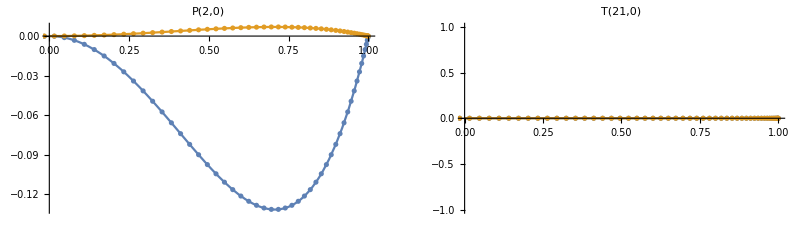

```mathematica
(* plot chosen component *)
data=NChebevalC[First[𝒱]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
p1=Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}],PlotLabel->First[𝒱]];
data=NChebevalC[Last[𝒱]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
p2=Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}],PlotLabel->Last[𝒱]];
GraphicsRow[{p1,p2}]
```

## Plot fields

```mathematica
ClearAll[up,upint,urint,ucint,upintconj,ucintconj,urintconj,uout]
gridr=N@Subdivide[Sequence@@Sprouts`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Sprouts`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[eigv⟦mode⟧,subset,1,Sprouts`layout⟦1⟧,Sprouts`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[upint[ℓ,𝓂][#] (1/#+logρ'[#])+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[upintconj[ℓ,𝓂][#] (1/#+logρ'[#])+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ]
];
uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utint[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Sprouts`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData["ThermometerColors"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-max,max} ]]&),ColorFunctionScaling->False,opts]]
```

```mathematica
gridN2=N2[gridr]⊗Y[0,0,gridθ,0]/.N0->0;
```

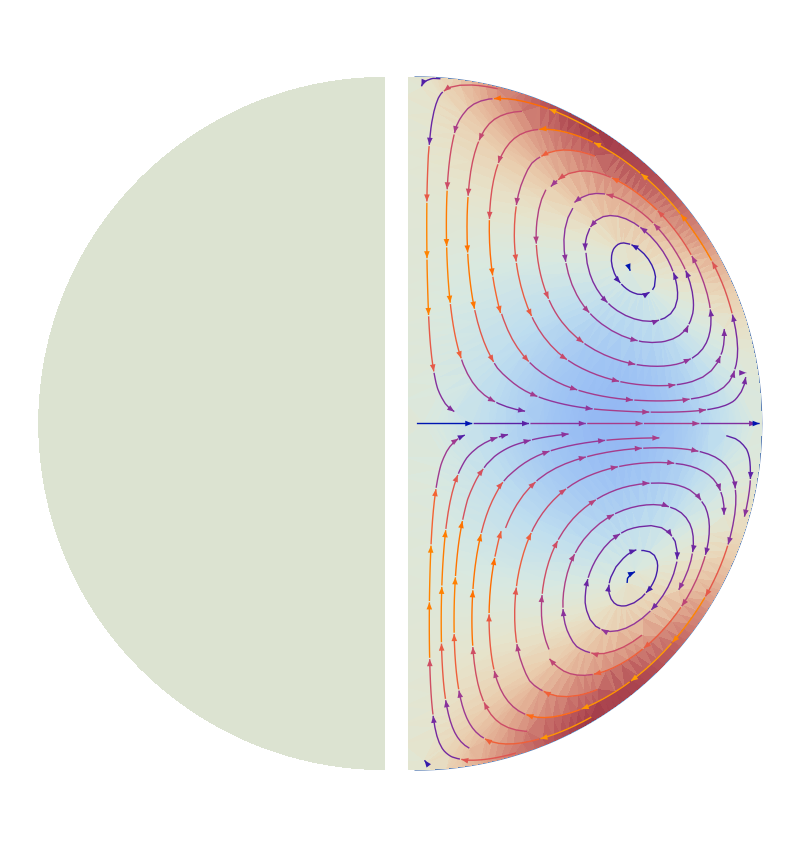

```mathematica
Needs["MaTeX`"]
plot=Show[
GraphicsGrid[{{
Show[MeridPlot[-gridr,gridθ,gridN2,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->20,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["N(r)^2",Magnification->1.5]],
Show[StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["\\text{Displacement}",Magnification->1.5]]}},Spacings->-40],PlotLabel->MaTeX["\\lambda",Magnification->1.5]==MaTeX[Chop@N[eig⟦pos⟧,4],Magnification->1.5](*MaTeX["\\lambda="<>ToString[Chop@N[eig⟦pos⟧,5]],Magnification->1.5]*)]
```

```mathematica
Export["~/Desktop/i-mode_m=0_l=4.pdf",plot,ImageSize->350,ImageResolution->400]
```

~/Desktop/i-mode_m=0_l=4.pdf